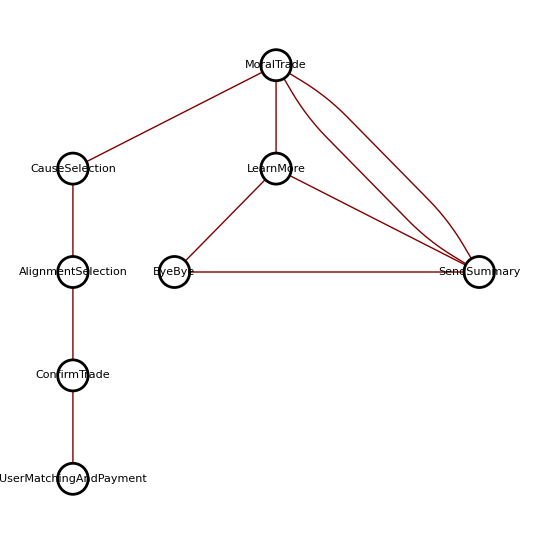

```mathematica
GraphPlot[{{MoralTrade->CauseSelection,"Yes"},{MoralTrade->LearnMore,"No"},{MoralTrade-> SendSummary, "Huh?"}, {CauseSelection -> AlignmentSelection, "GunRights/AbortionRights/Etc"}, 
{AlignmentSelection -> ConfirmTrade, "Positive/Negative/Neutral"}, 
{ConfirmTrade -> UserMatchingAndPayment, "Confirm"},
{LearnMore -> SendSummary, "Yes"}, {LearnMore -> ByeBye, "No"}, {SendSummary -> MoralTrade, ""}, {SendSummary -> ByeBye, "No"}},
DirectedEdges->True,
VertexRenderingFunction->({{White,Disk[#,0.15]},AbsoluteThickness[2],Circle[#,0.15],If[MatchQ[#2,A|B],Circle[#,0.12],{}],Text[#2,#]}&),
VertexCoordinateRules->{
MoralTrade->{4,7}, 
LearnMore->{4,6},
CauseSelection->{2,6},
SendSummary->{6,5},
AlignmentSelection->{2,5},
ConfirmTrade->{2,4},
UserMatchingAndPayment->{2,3},
ByeBye->{3,5}}]
```

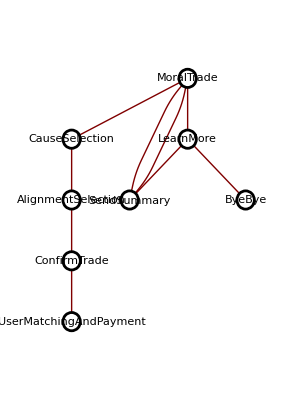

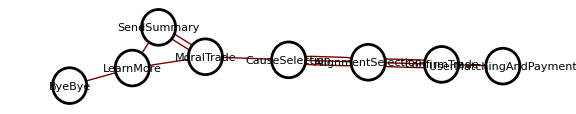

```mathematica
Show[%26,ImageSize->Large]
```